```mathematica
makeComplex[reals_,imags_] :=
Module[{realparts = reals, imagparts = imags},
complexPoints = Table[0, {i, 1, Length[realparts]}, {j, 1, Length[imagparts]}];
For[i = 1, i ≤ Length[realparts],i++,
For[j=1, j≤Length[imagparts],j++,
complexPoints[[i]][[j]] = realparts[[i]] + I*imagparts[[j]];
]
]
]
```

```mathematica
julia[z_, c_] :=
Module[{temp = z},
lim = 10^100;
n=40;
For[it=0,it<n, it++,
temp = temp^2 + c;
If[temp>lim, 
Break[]
]
];
juliapoint = temp
]
```

```mathematica
makeJuliaFractal[cReal_ ,cImag_, range_, incr_]:=
Module[{cR = cReal, cI=cImag, bound = range, step = incr},
iterations = 40;
c = cR + I*cI;
reals = Range[-bound,bound,step];
imaginaries = Range[-bound,bound,step];

juliaSet = Table[{0,0}, {k, 1, Length[reals]*Length[imaginaries]}];

(*makeComplex[reals,imaginaries];
*)(*Print[complexPoints];*)

jp =1;
For[i=1,i<=Length[reals],i++,
For[j=1,j≤Length[imaginaries],j++,
complexpoint = reals[[i]] + I*imaginaries[[j]];
juliapoint = julia[complexpoint,c];
(*Print[juliapoint];*)
If[Abs[juliapoint] ≤2,
juliaSet[[jp]] = {Re[complexpoint],Im[complexpoint]};
];
jp += 1;
]
];

(*Print[juliaSet];
*)ListPlot[juliaSet,PlotStyle->PointSize[0.01],Axes->False,Frame->False,FrameLabel->None,GridLines->None,AspectRatio->1,PlotRange->{{-2,2},{-2,2}}]
]

(*
1
c_real=-0.77
  c_imag=0.15


2
c_real=-0.81
c_imag=-0.1795

3
c_real=-0.04
c_imag=-0.684

4
c_real=-0.755
c_imag=0.05
*)
```

Greater::nord: Invalid comparison with -0.04 + 7.316\ ⅈ attempted.

Greater::nord: Invalid comparison with -53.5623 - 1.26928\ ⅈ attempted.

Greater::nord: Invalid comparison with 2867.26  + 135.287\ ⅈ attempted.

General::stop: Further output of Greater :: nord will be suppressed during this calculation.

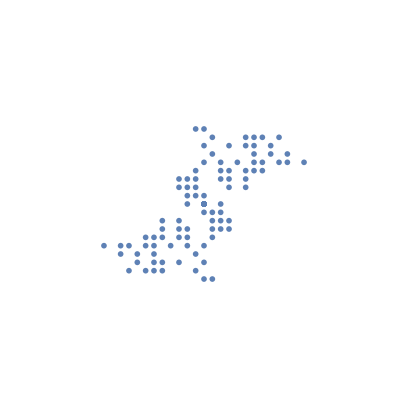

```mathematica
makeJuliaFractal[-0.04, -0.684, 2, 0.1]
```